Dado PI e PO, rint e rext, faz o cálculo da tensão radial e tangencial

```mathematica
ComputeRadialAndTangetialStress[r_,ri_,re_,PI_,PO_]:=Block[{sigr,sigtheta},
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigtheta=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));
{sigr,sigtheta}
];
ComputeRadialAndTangetialStress2[r_,ri_,re_,PI_,PO_,FZ_]:=Block[{ez,sigrr,sigtt,sigzz,a,b,Pa,Pb,nu=0.30,young=3 10^7},
a=ri;
b=re;
Pa=PI;
Pb=PO;
ez=FZ/(Pi young(b^2-a^2))-(2nu)/young(Pa a^2 -Pb b^2)/(b^2-a^2);
sigrr=(Pa a^2 -Pb b^2)/(b^2-a^2)-(a^2 b^2 (Pa-Pb))/((b^2-a^2)r^2);
sigtt=(Pa a^2 -Pb b^2)/(b^2-a^2)+(a^2 b^2 (Pa-Pb))/((b^2-a^2)r^2);
sigzz=2 nu (Pa a^2 -Pb b^2)/(b^2-a^2)+young ez;
{sigrr,sigtt,sigzz}
];
di=12.376;
de=14;
{sigr,sigt,sigz}=ComputeRadialAndTangetialStress2[di/2 ,di/2,de/2,8237,3629,1.312705856587157*^6]
sigz Pi/4( de^2-di^2)
```

{-8237.,33933.,39019.6}

1.31271×10^6

```mathematica
sigrr=(Pa a^2 -Pb b^2)/(b^2-a^2)-(a^2 b^2 (Pa-Pb))/((b^2-a^2)r^2);
sigtt=(Pa a^2 -Pb b^2)/(b^2-a^2)+(a^2 b^2 (Pa-Pb))/((b^2-a^2)r^2);
sigzz=2 nu (Pa a^2 -Pb b^2)/(b^2-a^2)
```

(2 nu (a^2 Pa-b^2 Pb))/(-a^2+b^2)

```mathematica
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigtheta=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));
```

```mathematica
Simplify[sigtheta/.r->ri]
```

(-2 PO re^2+PI (re^2+ri^2))/(re^2-ri^2)

```mathematica
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2 ,di/2,de/2,8237,3629]
{sigr,sigt,sigz}=ComputeRadialAndTangetialStress2[di/2 ,di/2,de/2,8237,3629]
sigz Pi/4( de^2-di^2)
nu(sigr+sigt)Pi/4( de^2-di^2)
```

{-8237.,33933.}

Set::shape: Lists {sigr,sigt,sigz} and ComputeRadialAndTangetialStress2[6.188,6.188,7,8237,3629] are not the same shape.

ComputeRadialAndTangetialStress2[6.188,6.188,7,8237,3629]

1.31271×10^6

864471. nu

Dado dint, dext, PI e PO, faz o cálculo da tensão axial (TA) devido ao efeito poisson (Balão)

```mathematica
ComputeFballoning[di_,de_,Pint_,Pext_,nu_]:=Block[{sigr,sigt,Fballoning},
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2 ,di/2,de/2,Pint,Pext];
Fballoning=nu(sigr+sigt)Pi/4( de^2-di^2);
Fballoning
];
```

Dado dint, dext e dT, calcula a TA devido à temperatura

```mathematica
ComputeFtemperature[de_,di_,TM_,TPM_]:=Block[{young = 3 10^7,alfa=12.42 10^-6,ΔT,T1,f,fp,T2,Ftemperature},
ΔT= (TPM-TM) ;
Ftemperature=-young alfa ΔT Pi/4(de^2-di^2);
Ftemperature
]
```

Calcula-se o alongamento equivalente e a reação de apoio

```mathematica
(*ComputeAxialReaction[Force_,de_,di_]:=Block[{tabf,df,n=1000,DL,DF,young = 3 10^7,area,L=1},
area=Pi/4(de^2 -di^2);
df=Force/n;
tabf=Table[Force-df i,{i,1,n}];
PrependTo[tabf,Force];
DL=1/ (young area) Sum[tabf[[i]] (L/n),{i,1,n}];
DF=young DL/L  area;
DF
];*)
```

```mathematica
ComputeAxialReaction[Force_,area_,L_]:=Block[{tabf,df,Steps=1000,DL,DF,young =3 10^7,dx,x,w,i},
dx=L/Steps;
DL=0.;
x=0.;
w=Force/L;
For[i=1,i≤Steps,i++,
DL+=w(2 x dx+dx^2)/2;
x+=dx;
]; 
DL=DL/(young area);
(*Print["DL = ",DL];*)
DF=young DL/L  area
];
R=0;
w=3;
stepss=10;
dx=9/stepss;
f=0;
x=0.;
area=0.1 0.2;
For[jj=1,jj≤stepss,jj++,
f=w dx;
R+=ComputeAxialReaction[f,area,dx];
f=x w;
x+=dx;
];
R
```

13.5

```mathematica
ComputeReaction[Force_,area_,L_]:=Block[{tabf,df,DL,DF,young =3 10^7,dx,x,w,i},
w=Force/L;
DL=w L^2/(2 young area);
young DL/L  area
];
```

```mathematica
ComputeReaction[3 9,0.1 0.2,9]
```

13.5

```mathematica
ComputeBalooningFreePart[pipedatavec_,PiData_,PeData_,Lcement_]:=Block[{bal,pipe,de,di,i,ndata,L1,young,nu,weigthperfeet,L2,sigy},
bal=0;
pipe=1;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=pipedatavec[[pipe]];
ndata=Length[PiData];
For[i=ndata,i≥1,i--,
If[L1>PiData[[i,2]],
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=pipedatavec[[pipe]];
];
If[PiData[[i,2]]<=Lcement,
bal+=ComputeFballoning[di,de,PiData[[i,1]],PeData[[i,2]],nu];
];
];
bal/ndata
]
```

Discretização do tubular(Comprimento e Pressão)

```mathematica
ExpandTable[table_,ntimes_]:=Block[{i,deltaL,deltaP,newtab={},j,pi,l,lastp=0,lastl=0,tol=10^-8},
For[j=2,j≤Length[table],j++,
deltaL=(table[[j,2]]-table[[j-1,2]])/ntimes;
deltaP=(table[[j,1]]-table[[j-1,1]])/ntimes;
If[deltaP<0.1,deltaP=0.1];
If[deltaL<0.1,deltaL=0.1];
pi=table[[j-1,1]];
l=table[[j-1,2]];
For[i=1,i≤ntimes,i++,

l+=deltaL;
pi+=deltaP;
If[(pi-lastp)>tol &&(l-lastl)>tol,
AppendTo[newtab,{pi,l}];
];
lastp=pi;
lastl=l;
];
];
newtab
]
```

Discretização do tubular(Pressão)

```mathematica
ExpandTableOne[table_,ntimes_]:=Block[{i,deltaL,deltaP,newtab={},j,pi,l},
For[j=2,j≤Length[table],j++,
deltaP=(table[[j]]-table[[j-1]])/ntimes;
pi=table[[j]];
For[i=1,i≤ntimes,i++,
AppendTo[newtab,pi];
pi+=deltaP;
];
];
newtab
]
```

Cortando o vetor no ponto desejado (lcut)

```mathematica
FilterData[data_,lcut_,topdown_]:=Block[{newdata={},i},
i=1;
If[topdown==1,
While[data[[i,2]]<=lcut,
AppendTo[newdata,data[[i,1]]];
i++;
];
,
i=Length[data];
While[data[[i,2]]>=lcut,
AppendTo[newdata,data[[i,1]]];
i--;
];

];
newdata
]
```

```mathematica
FilterData[data_,lcut_]:=Block[{newdata={},i},
i=1;
While[data[[i,2]]<=lcut,
AppendTo[newdata,data[[i,1]]];
i++;
];

newdata
]
```

Inverte a ordem do vetor(traz para frente e vice versa)

```mathematica
InvertOrder[ax_]:=Block[{newax,i},
newax=Table[0,{Length[ax]}];
For[i=1,i<Length[ax],i++,
newax[[i]]=ax[[Length[ax]-i]];
];
newax[[Length[ax]]]=ax[[1]];
newax
];
```

Cálculo das pressões para o caso do poço cheio de gás

```mathematica
IntermediateKickLoadingFullOfGas[h_,LDA_,Linter_,Lnext_,Lcement_,globaldensitydata_,P0_]:=Block[{Psap,rhocement,sol,rhonext,rhogas,SurfacePressure,rhowater,hgas,hmud,Pib,Ptemp,hgi,Pob,eq1,eq2,ppgtopsi=0.051948,rhoHC,rhoPF},
{rhogas,rhowater,rhocement,rhonext,rhoHC,rhoPF,SurfacePressure,Psap}=globaldensitydata;
(*P0=LDA rhowater ppgtopsi;*)
hmud=0;
hgas=Lnext;
Pib=Psap-ppgtopsi rhogas (Linter-h);
If[h>Lcement,
Pob=P0+ppgtopsi( rhowater (Lcement-LDA)+ rhocement (h-Lcement));
,
Pob=ppgtopsi rhowater (h-LDA)+P0;
];
{Pib,Pob}
];
```

Cálculo das pressões para o caso de um vazamento na coluna de produção

```mathematica
IntermediateTubingLeak[h_,LDA_,Lzpr_,Lcement_,globaldensitydata_]:=Block[{Pzpr,rhoPF,,Pcabpt,rhoHC,Psap,rhocement,sol,rhonext,rhogas,SurfacePressure,rhowater,hgas,hmud,Pib,Ptemp,hgi,Pob,P0,eq1,eq2,ppgtopsi=0.051948},
{rhogas,rhowater,rhocement,rhonext,rhoHC,rhoPF,SurfacePressure,Pzpr}=globaldensitydata;
Pcabpt=Pzpr-ppgtopsi rhoHC (Lzpr-LDA);(*OK*)
P0=LDA rhowater  ppgtopsi;
Pib=Pcabpt+ppgtopsi rhoPF(h-LDA);
If[h>Lcement,
Pob=P0+ppgtopsi( rhowater (Lcement-LDA)+ rhocement (h-Lcement));
,
Pob=ppgtopsi rhowater (h-LDA)+P0;
];
{Pib,Pob}
];
```

Cálculo das pressões para o caso de perda de circulação

```mathematica
FullEvacIntermediate[h_,LDA_,Lnext_,globaldensitydata_]:=Block[{ha,hm1,hm2,ExtPress,InterPress,Linter,sz,hogas,rhowater,rhocement,rhonext,rhoHC,rhoPF,P0,Psap,rhogas,Pib,Pob},
{rhogas,rhowater,rhocement,rhonext,rhoHC,rhoPF,P0,Psap}=globaldensitydata;
InterPress=0;
ExtPress=P0+0.052 rhonext (h-LDA);
{InterPress,ExtPress}
];
```

```mathematica
SetData[currentpipedata_]:=Block[{de,di,t,sigy,young,nu,weigthft,nfactorStewart},
de=currentpipedata[[1]];
di=currentpipedata[[5]];
weigthft=currentpipedata[[2]];
t=currentpipedata[[4]];
sigy=currentpipedata[[13]];
young=currentpipedata[[11]];
nu=currentpipedata[[12]];
nfactorStewart=currentpipedata[[14]];
{de,di,t,sigy,young,nu,weigthft,nfactorStewart}
];
```

Cálculo das pressões ao longo do poço

```mathematica
ComputePressures[Lsap_,Lnext_,Lcement_,LDA_,PipesData_,globaldensitydata_,steps_,case_]:=Block[{npipes,PI={},PO={},i,j,Pib,Pob,counter,h,deltah,Lsection,currentpipedata,de,di,t,sigy,young,nu,weigthperfeet,n},
npipes=Length[PipesData];
h=Lsap;
For[i=npipes,i≥ 1,i--,
Lsection=PipesData[[i]][[2]]-PipesData[[i]][[1]];
deltah=Lsection/steps;
currentpipedata=PipesData[[i,3]];
{de,di,t,sigy,young,nu,weigthperfeet,n}=SetData[currentpipedata];

For[j=1 ,j≤steps,j++,
Switch[case,1,
P0=LDA 3.79 0.052;
{Pib,Pob}=IntermediateKickLoadingFullOfGas[h,LDA,Lsap,Lnext,Lcement,globaldensitydata,P0];
,2,
{Pib,Pob}=IntermediateTubingLeak[h,LDA,Lnext,Lcement,globaldensitydata];
,3,
{Pib,Pob}=FullEvacIntermediate[h,LDA,Lnext,globaldensitydata];
];
PrependTo[PI,{Pib,h/3.28}];
PrependTo[PO,{Pob,h/3.28}];
h-=deltah;
];

];
{PI,PO}
];
```

Cálculo da força pistão

```mathematica
ComputePistonForce[PiData_,PeData_,PipeData_]:=Block[{i,olddi,oldde,pipe,de,di,young,nu,weigthperfeet,L1,L2,PistonForce=0,sigy},
pipe=1;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[1]];
For[i=Length[PipeData],i>1,i--,
olddi=di;
oldde=de;
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
PistonForce+=Pi/4 (olddi^2-di^2) PiData[[i,1]]-Pi/4 (oldde^2-de^2) PeData[[i,1]];
];
PistonForce
];
```

```mathematica
Barlow[sigy_,de_,di_]:=Block[{t=(de-di)/2},0.875 2 sigy/(de/t)]
```

Calcula a resistência do tubular à ruptura e ao colapso de acordo com a API BUL 5C3

```mathematica
ComputePipeStrength[siga_,sigy_,de_,di_,young_,nu_]:=Block[{t=(de-di)/2,BurstStrength, ColapseStrength,dt,Ypa,A,B,C,F,G,range1,range2,range3},
BurstStrength=0.875 2 sigy/(de/t);
dt=de/t;
Ypa=sigy (Sqrt[1-3/4 (siga/sigy)^2]-1/2 siga/sigy);
A=2.8762+0.10679 10^-5 Ypa+0.21301 10^-10 Ypa^2-0.53132 10^-16 Ypa^3;
B=0.026233+0.50609 10^-6 Ypa;
C=-465.93+0.030867 Ypa-0.10483 10^-7 Ypa^2+0.36989 10^-13 Ypa^3;
F=(46.95 10^6 ((3(B/A))/(2+B/A))^3)/(Ypa((3(B/A))/(2+B/A)-B/A)(1-(3(B/A))/(2+B/A))^2);
G=F B/A;
range1=(2+B/A)/(3 B/A);

If[dt≥ range1,

ColapseStrength=(2 young)/(1-nu^2) 1/(dt(dt-1)^2);
];
range2=(Ypa(A-F))/(C+Ypa(B-G));
If[range2≤ dt≤ range1,

ColapseStrength= (F/dt-G)Ypa;
];
range3=(Sqrt[(A-2)^2+8(B+C/Ypa)]+(A-2))/(2(B+C/Ypa));
If[(range3≤ dt≤ range2),

ColapseStrength=Ypa (A/dt-B)-C;
];

If[dt≤ range3,

ColapseStrength=2Ypa (dt-1)/dt^2;
];
{BurstStrength,ColapseStrength}
];
```

Calcula a tensão de von Mises

```mathematica
ComputeVonMises[sigr_,sigt_,siga_]:=Block[{sig,S,J2},
sig={{sigr,0,0},{0,sigt,0},{0,0,siga}};
S=sig-1/3 Tr[sig] IdentityMatrix[3];
(*Print[S];*)
J2=1/2 Tr[S.S];
Sqrt[3 J2]
];
```

```mathematica
ComputeVonMises[sigrr ,sigtt,sigaa]//FullSimplify
```

√((-2 a^2 b^2 r^4 (Pa+sigaa) (Pb+sigaa)+b^4 r^4 (Pb+sigaa)^2+a^4 (3 b^4 (Pa-Pb)^2+r^4 (Pa+sigaa)^2))/((a^2-b^2)^2 r^4))

Calcula os fatores de segurança

```mathematica
ComputeSafetyFactors[PipeData_,AxialForce_,Pint_,Pext_]:=Block[{APISF={}, BarlowSF={},i,barlow,api,de,di,young,nu,weigthperfeet,L1,L2,pipe=1,sigy,VMSF={},sigr,sigt,area,VMStress},

{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
For[i=Length[Pint]-1,i>1,i--,
If[L1>Pint[[i,2]],
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
];
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2,di/2,de/2,Pint[[i,1]],Pext[[i,1]]];
area=Pi/4 (de^2 -di^2);
VMStress=ComputeVonMises[sigr,sigt,AxialForce[[i,1]]/area];
barlow=Barlow[sigy,de,di];
api=ComputePipeStrength[AxialForce[[i,1]]/area,sigy,de,di,young,nu];
AppendTo[BarlowSF,{api[[1]]/(Pint[[i,1]]-Pext[[i,1]]),-Pint[[i,2]]}];
AppendTo[APISF,{api[[2]]/(Pint[[i,1]]-Pext[[i,1]]),-Pint[[i,2]]}];
AppendTo[VMSF,{sigy/VMStress,-Pint[[i,2]]}];
];
{BarlowSF,APISF,VMSF}
];
```

Calcula a tensão axial

```mathematica
ComputeAxialStress[PiData_,PeData_,PipeData_,Lcement_,Ltotal_,Ti_,Tp_]:=Block[{deltabal,VecPicement,VecPecement,FPistn,FTempn,Fballoningn,Fballoningn1,AxialForceVec,WeigthFreePart,de,di,young,nu,weigthperfeet,BalloningForce=0,PistonForce=0,TemperatureForce=0,WeigthForce=0,dh=0,AxialForce={},ReactionForce=0,MeanPiFree=0,MeanPeFree=0,VecPi,VecPe,i,L1,L2,olddi,pipe,oldde,MeanTiFree,MeanTpFree,VecTi,VecTp,PistonForceJoints,sigy,PI,PO,Aint,Aext,OldAint,OldAext,ii,sumpi,sumpe,LDA=PiData[[1,2]],sumti,sumtp,PistTrue=False},

{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[1]];
pipe=1;
AxialForceVec=Table[0,{Length[PiData]},{2}];
For[i=Length[PiData],i>1,i--,
PI= PiData[[i,1]];
PO= PeData[[i,1]];
Aint=Pi/4 di^2 ;
Aext=Pi/4 de^2 ;
(*No primeiro passo calcula o efeito pistão de fundo e a reação na interface do cimento*)

(*mudanca de tubular e aplicação do efeito pistão*)
If[L1>PiData[[i,2]],
OldAint=Aint;
OldAext=Aext;
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
Aint=Pi/4 di^2 ;
Aext=Pi/4 de^2 ;
PistonForce=(OldAint-Aint)PI-(OldAext-Aext) PO;
PistTrue=True;
];


If[PiData[[i,2]]>=Lcement,
(*Trecho Cimentado*)
dh=(PiData[[i,2]]-PiData[[i-1,2]])3.28;
If[i==Length[PiData],
(*Calculando o valor da força axial no fundo do  poço, na base do cimento. Apenas o primeiro passo*)
(*BalloningForce=ComputeFballoning[di,de,(PiData[[i,1]]),(PeData[[i,1]]),nu];*)
(*Geting pressure data only at the cement part*)
VecPicement=FilterData[PiData,Lcement,0];
VecPecement=FilterData[PeData,Lcement,0];
(*Cálculo da força no fundo em decorrência do efeito poisson*)
(*BalloningForce=ComputeFballoning[di,de,Mean[VecPicement],Mean[VecPecement],nu];*)
(*BalloningForce=ComputeFballoning[di,de,(PiData[[i,1]]),(PeData[[i,1]]),nu];
Fballoningn=BalloningForce;
BalloningForce=ComputeFballoning[di,de,(PiData[[i-1,1]]),(PeData[[i-1,1]]),nu];
BalloningForce=(BalloningForce+Fballoningn)/2;*)
BalloningForce=ComputeFballoning[di,de,Mean[VecPicement],Mean[VecPecement],nu];
Print["MEanBalloningForce = ",BalloningForce];
Fballoningn=ComputeFballoning[di,de,(PiData[[i,1]]),(PeData[[i,1]]),nu];
BalloningForce=ComputeFballoning[di,de,(PiData[[i-1,1]]),(PeData[[i-1,1]]),nu];
deltabal=-Fballoningn+BalloningForce;

PistonForce= PI Aint -PO Aext;

Print["deltabal = ",deltabal];
Print["PiData[[i,1]] = ",PiData[[i,1]]];
Print["PeData[[i,1]] = ",PeData[[i,1]]];
Print["BalloningForce = ",BalloningForce];
Print["Fballoningn = ",Fballoningn];
Print["PistonForce = ",PistonForce];
Print["WeigthForce = ",WeigthForce];

AxialForceVec[[i]]={PistonForce+Fballoningn+WeigthForce,-PiData[[i,2]]};
If[PiData[[i,1]]>PeData[[i,1]],
AxialForceVec[[i]]={1.42PistonForce,-PiData[[i,2]]};
,
AxialForceVec[[i]]={0.70PistonForce,-PiData[[i,2]]};
];
(*AxialForceVec[[i]]={-285331,-PiData[[i,2]]};
AxialForceVec[[i]]={-1126742,-PiData[[i,2]]};*)
Print["i= ",i];
Print["AxialForceVec[[i]] = ",AxialForceVec[[i]]];

,
(*Calculando o valor da força axial nos demais trechos cimentados como sendo Fan1=Fan+ΔFb+ΔFw*)
Fballoningn=BalloningForce;
BalloningForce=ComputeFballoning[di,de,(PiData[[i,1]]),(PeData[[i,1]]),nu];
deltabal=-Fballoningn+BalloningForce;

If[PistTrue==False,

AxialForceVec[[i]]={AxialForceVec[[i+1,1]]+deltabal+weigthperfeet dh,-PiData[[i,2]]};
,
(*delta do efeito pistão*)
(*Caso ocorra mudança de diâmetro dos tubos, esse efeito é considerado aqui*)
Print["PIST TRUE CEMENT"];
AxialForceVec[[i]]={AxialForceVec[[i+1,1]]+PistonForce,-PiData[[i,2]]};
];
PistTrue=False;
];

If[i==Length[PiData],
Print["First Cement Step"];
Print["di = ",di];
Print["de= ",de];
Print["Mean[VecPicement] = ",Mean[VecPicement]];
Print["Mean[VecPecement] = ",Mean[VecPecement]];

];
(*Print["i= ",i];
Print["AxialForceVec[[i]] = ",AxialForceVec[[i]]];*)
WeigthForce+=weigthperfeet dh;
flag=True;
,

(*Trecho Livre*)
If[flag==True,
WeigthForce=0.;
Print["Last Cement Step"];
Print["BalloningForce = ",BalloningForce];
Print["PistonForce = ",PistonForce];
Print["WeigthForce = ",WeigthForce];
Print["First Free Step"];
PistonForceJoints=ComputePistonForce[PiData,PeData,PipeData];(*Efeito Pistão Mudança de Tubulares Trecho Livre*)
VecPicement=FilterData[PiData,Lcement,1];
VecPecement=FilterData[PeData,Lcement,1];
BalloningForce=ComputeFballoning[di,de,Mean[VecPicement],Mean[VecPecement],nu];
WeigthFreePart=3.28((2150-1933)88.2+(4803-2150)115);
(*ReactionForce=ComputeAxialReaction[WeigthFreePart+BalloningForce+PistonForceJoints,area,3.28(Lcement-LDA)];*)(*Reação Interface Cimento*)
(*ReactionForce=ComputeReaction[WeigthFreePart+BalloningForce+PistonForceJoints,area,3.28(Lcement-LDA)];*)
ReactionForce=Abs[ComputeReaction[BalloningForce+PistonForceJoints,area,3.28(Lcement-LDA)]]1.42;
AxialForceVec[[i]]={AxialForceVec[[i+1,1]]+ReactionForce,-PiData[[i,2]]};
,
dh=(PiData[[i,2]]-PiData[[i-1,2]])3.28;

If[PistTrue==False,
AxialForceVec[[i]]={AxialForceVec[[i+1,1]]+weigthperfeet dh,-PiData[[i,2]]};
,
AxialForceVec[[i]]={AxialForceVec[[i+1,1]]-PistonForce,-PiData[[i,2]]};
];
PistTrue=False;

];

flag=False;
];
WeigthForce+=weigthperfeet dh;
];
Print["WeigthForce = ",WeigthForce];
AxialForceVec=Delete[AxialForceVec,1];
AxialForceVec
];
```

```mathematica
L={1933.04,1946.97,1947.03,2133.60,2149.97,2150.03,2438.40,2743.20,3048.00,3172.97,3173.03,3352.80,3422.84,3422.96,3423.03,3450.00,3657.60,3810.00,3962.40,4267.20,4572.00,4802.98,4803.04,4876.80,5181.60,5302.97};
triaxialSF={1.655,1.660,1.660,1.735,1.741,2.477,2.661,2.867,3.114,3.230,3.230,3.432,3.520,3.520,3.520,3.555,3.852,4.105,4.394,5.115,6.126,7.210,7.417,7.667,8.789,8.789};
burstSF={1.369,1.374,1.374,1.438,1.444,2.044, 2.196, 2.364, 2.567, 2.662, 2.662, 2.827, 2.899, 2.899,2.899, 2.928, 3.171, 3.377, 3.612, 4.200, 5.021, 5.897, 5.898, 6.111, 7.188, 7.188};
triaxialSFvec=Table[{triaxialSF[[i]],-L[[i]]},{i,1,Length[L]}];
burstSFvec=Table[{burstSF[[i]],-L[[i]]},{i,1,Length[L]}];
AxialStress={1219092,1215040,1215040,1161044,1156298,1143218,1034406,919406,804406,757244,757244,689406,662978,662920,662920,652732,574406,516906,459406,344406,229406,142251,-21791,-49413,-162492,-285331};
VecPi={7699.40,7705.68,7705.70,7789.65,7797.02,7797.04,7926.79,8063.94,8201.08,8257.31,8257.33,8338.22,8369.74,8369.79,8369.82,8381.96,8475.36,8543.94,8612.51,8749.65,8886.79,8990.71,8990.74,9023.93,9161.08,9215.69};
VecPe={1249.56,1277.36,1277.48,1649.51,1682.16,1682.28,2257.31,2865.10,3472.90,3722.09,3722.21,4080.69,4220.37,4220.61,4220.73,4274.52,4688.49,4992.38,5296.28,5904.08,6511.87,6972.44,6972.54,7077.28,7510.00,8522.08};
Ti={4.44,5.15,5.16,14.68,15.52,15.52,30.24,45.79,61.35,67.72,67.73,71.46,72.11,72.11,72.11,72.35,74.25,75.65,77.04,79.83,82.62,84.73,84.73,85.40,88.19,90.29};
Tp={4.44,5.15,5.16,14.68,15.52,15.52,30.24,45.79,61.35,67.72,67.73,71.46,72.11,72.11,72.11,72.35,74.25,75.65,77.04,79.83,82.62,84.73,84.73,85.40,88.19,90.29};
(*Tp=Table[90.29,{i,1,Length[Tp]}];*)
VecPiBeforeCement={7699.40,7705.68,7705.70,7789.65,7797.02,7797.04,7926.79,8063.94,8201.08,8257.31,8257.33,8338.22,8369.74,8369.79,8369.82,8381.96,8475.36,8543.94,8612.51,8749.65,8886.79,8990.71};
VecPeBeforeCement={1249.56,1277.36,1277.48,1649.51,1682.16,1682.28,2257.31,2865.10,3472.90,3722.09,3722.21,4080.69,4220.37,4220.61,4220.73,4274.52,4688.49,4992.38,5296.28,5904.08,6511.87,6972.44};
tablePi=Table[{VecPi[[i]],-L[[i]]},{i,1,Length[L]}];ExpandTable
stress=Table[{AxialStress[[i]],-L[[i]]},{i,1,Length[L]}];
```

ExpandTable

MEanBalloningForce = -22341.5

deltabal = 895.37

PiData[[i,1]] = 9215.69

PeData[[i,1]] = 8501.84

BalloningForce = -119193.

Fballoningn = -120088.

PistonForce = -200147.

WeigthForce = 0

i= 2492

AxialForceVec[[i]] = {-284209.,-5302.97}

First Cement Step

di = 12.376

de= 14

Mean[VecPicement] = 9071.48

Mean[VecPecement] = 7330.85

Last Cement Step

BalloningForce = 5365.18

PistonForce = -200147.

WeigthForce = 0.

First Free Step

WeigthForce = 1.0626×10^6

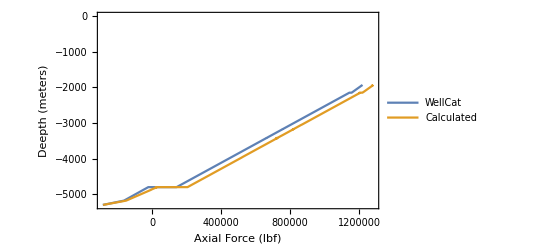

```mathematica
tablePi=Table[{VecPi[[i]],L[[i]]},{i,1,Length[L]}];
tablePe=Table[{VecPe[[i]],L[[i]]},{i,1,Length[L]}];
tableTi=Table[{Ti[[i]],L[[i]]},{i,1,Length[L]}];
tableTp=Table[{Tp[[i]],L[[i]]},{i,1,Length[L]}];
n=100;
PiData=ExpandTable[tablePi,n]; 
PeData=ExpandTable[tablePe,n];
TiData=ExpandTable[tableTi,n];
TpData=ExpandTable[tableTp,n];
Lcement=4803;
Ltotal=5303;
LDA=1933;
weigth=0;
young=3 10^7;
weigthperfeet=115;
di=12.376;
de=14;
nu=0.3;
pipedata={de,di,young,nu,weigthperfeet};
pipedatavec={
{14,12.376,young,nu,115,2150,5303,125000},
{13.625,12.376,young,nu,88.2,1933,2150,110000}
};
ax=ComputeAxialStress[PiData,PeData,pipedatavec,Lcement,Ltotal,TiData,TpData];
newax=InvertOrder[ax];

ListLinePlot[{stress,newax},Frame->True,FrameLabel->{{"Deepth (meters)",""},{"Axial Force (lbf)",""}},PlotLegends->{"WellCat","Calculated"}]
```

```mathematica
285331/-200147.4926727733
```

-1.4256

```mathematica
F=259000-10021
L=3.28(Lcement-LDA)
delta=(F/L)L^2/(2 young As)
young delta/L As
```

248979

9413.6

39.0631/As

124490.

```mathematica
ComputeFballoning[12.376,14,9071.47,7330.850,0.3]
```

-22342.1

```mathematica
ComputeBalooningFreePart[pipedatavec,PiData,PeData,Lcement]
```

258514.

```mathematica
ComputePistonForce[PiData,PeData,pipedatavec]
```

-10171.2

```mathematica
ComputeAxialReaction[WeigthFreePart-bal-PistonForceJoints,Pi/4 (de^2-di^2),3.28(4803-1933)]
```

0.000106229 (0.+4706.8 (-bal-PistonForceJoints+WeigthFreePart))

```mathematica
Pi/4 (de^2-di^2)
```

33.6422

```mathematica
pipedatavec
```

{{14,12.376,30000000,0.3,115,2150,5303,125000},{13.625,12.376,30000000,0.3,88.2,1933,2150,110000}}

```mathematica
de
```

14

```mathematica
di
```

12.376

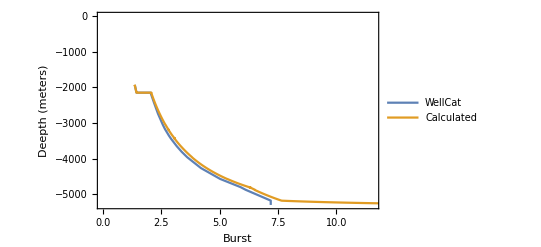

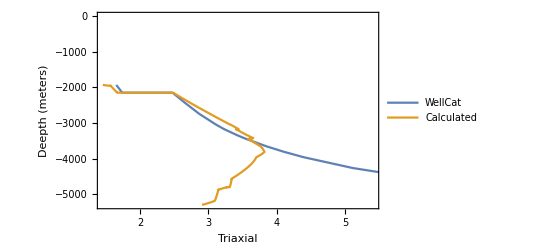

```mathematica
{barlowsf,apisf,vmsf}=ComputeSafetyFactors[pipedatavec,newax,PiData,PeData];
ListLinePlot[{burstSFvec,barlowsf},Frame->True,FrameLabel->{{"Deepth (meters)",""},{"Burst",""}},PlotLegends->{"WellCat","Calculated"}]
ListLinePlot[{triaxialSFvec,vmsf},Frame->True,FrameLabel->{{"Deepth (meters)",""},{"Triaxial",""}},PlotLegends->{"WellCat","Calculated"}]
```

```mathematica
b
```

b

```mathematica
-1126742 1.42
```

-1.59997×10^6

```mathematica
-913885.7667021287/-1.599685019199173*^6
```

0.571291

MEanBalloningForce = -913886.

deltabal = 185.018

PiData[[i,1]] = 3078.95

PeData[[i,1]] = 12797.8

BalloningForce = -959626.

Fballoningn = -959811.

PistonForce = -1.59969×10^6

WeigthForce = 0

i= 2484

AxialForceVec[[i]] = {-1.11978×10^6,-5302.97}

First Cement Step

di = 12.376

de= 14

Mean[VecPicement] = 2529.15

Mean[VecPecement] = 11870.9

Last Cement Step

BalloningForce = -881187.

PistonForce = -1.59969×10^6

WeigthForce = 0.

First Free Step

WeigthForce = 1.0626×10^6

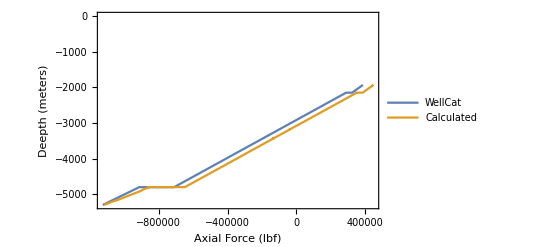

```mathematica
L={1933.04,1946.97,1947.03,2133.60,2149.97,2150.03,2438.40,2743.20,3048.00,3172.97,3173.03,3352.80,3422.84,3422.96,3423.03,3450.00,3657.60,3810.00,3962.40,4267.20,4572.00,4802.98,4803.04,4876.80,5181.60,5302.97};
AxialStress={387740,383688,383688,329692,324946,290064,181252,66252,-48748,-95909,-95909,-163748,-190176,-190234,-190234,-200421,-278748,-336248,-393748,-508748,-623748,-710903,-913884,-945470,-1074942,-1126742};
VecPi={3.29,3.32,3.32,3.64,3.66,3.66,4.16,4.68,5.19,5.41,5.41,5.71,5.83,5.83,5.83,5.88,274.68,534.40,794.15,1313.65,1833.10,2226.73,2226.83,2352.62,2872.05,3078.95};
VecPe={3854.56,3882.36,3882.48,4254.52,4287.16,4287.28,4862.32,5470.12,6077.92,6327.12,6327.24,6685.72,6825.40,6827.56,6828.65,7307.20,7926.40,8380.96,8835.52,9744.64,10653.76,11342.67,11342.85,11562.89,12472.01,12834.01};
Ti={4.44,5.15,5.16,14.68,15.52,15.52,30.24,45.79,61.35,67.72,67.73,71.46,72.11,72.11,72.11,72.35,74.25,75.65,77.04,79.83,82.62,84.73,84.73,85.40,88.19,90.29};
Tp={4.44,5.15,5.16,14.68,15.52,15.52,30.24,45.79,61.35,67.72,67.73,71.46,72.11,72.11,72.11,72.35,74.25,75.65,77.04,79.83,82.62,84.73,84.73,85.40,88.19,90.29};
(*Tp=Table[197,{i,1,Length[Tp]}];*)
stress=Table[{AxialStress[[i]],-L[[i]]},{i,1,Length[L]}];
tablePi=Table[{VecPi[[i]],L[[i]]},{i,1,Length[L]}];

tablePe=Table[{VecPe[[i]],L[[i]]},{i,1,Length[L]}];
tableTi=Table[{Ti[[i]],L[[i]]},{i,1,Length[L]}];
tableTp=Table[{Tp[[i]],L[[i]]},{i,1,Length[L]}];
n=100;
PiData=ExpandTable[tablePi,n];
PeData=ExpandTable[tablePe,n];
TiData=ExpandTable[tableTi,n];
TpData=ExpandTable[tableTp,n];
Lcement=4803;
Ltotal=5303;
weigth=0;
young=3 10^7;
weigthperfeet=115;
di=12.376;
de=14;
nu=0.3;
pipedata={de,di,young,nu,weigthperfeet};
pipedatavec={
{14,12.376,young,nu,115,2150,5303,125000},
{13.625,12.375,young,nu,88.2,1933,2150,110000}
};
ax=ComputeAxialStress[PiData,PeData,pipedatavec,Lcement,Ltotal,TiData,TpData];
newax=InvertOrder[ax];
ListLinePlot[{stress,newax},Frame->True,FrameLabel->{{"Deepth (meters)",""},{"Axial Force (lbf)",""}},PlotLegends->{"WellCat","Calculated"}]
```

```mathematica
alpha=12.42 10^-6
e=3 10^7;
```

0.00001242

```mathematica
de
```

14

Interpolation::inddp: The point 3.52 in dimension 1 is duplicated.

Interpolation[{{3.39,1933.18},{3.49,1933.32},{3.59,1933.46},{3.69,1933.6},{3.79,1933.74},{3.89,1933.88},{3.99,1934.02},{4.09,1934.15},{4.19,1934.29},{4.29,1934.43},2464,{3060.33,5292.05},{3062.4,5293.26},{3064.47,5294.47},{3066.54,5295.69},{3068.6,5296.9},{3070.67,5298.12},{3072.74,5299.33},{3074.81,5300.54},{3076.88,5301.76},{3078.95,5302.97}}]
 |  |  |  |

InterpolatingFunction[{{3854.84, 12834.}}, <>]

InterpolatingFunction::dmval: Input value {0.102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

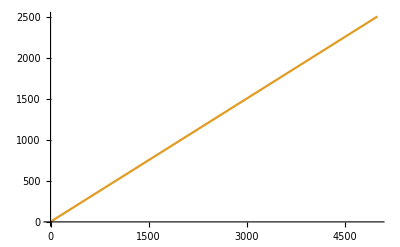

```mathematica
pi=Interpolation[PiData]
pe=Interpolation[PeData]
Plot[{pi[x],pe[x]},{x,0,5000}]
```

```mathematica
pi[2]
```

Interpolation[{{3.39,1933.18},{3.49,1933.32},{3.59,1933.46},{3.69,1933.6},{3.79,1933.74},{3.89,1933.88},{3.99,1934.02},{4.09,1934.15},{4.19,1934.29},{4.29,1934.43},{4.39,1934.57},2463,{3060.33,5292.05},{3062.4,5293.26},{3064.47,5294.47},{3066.54,5295.69},{3068.6,5296.9},{3070.67,5298.12},{3072.74,5299.33},{3074.81,5300.54},{3076.88,5301.76},{3078.95,5302.97}}][2]
 |  |  |  |

```mathematica
sigr
```

-8237.

```mathematica
sigr[2]
```

(-8237.)[2]

```mathematica
A
```

A

```mathematica
Clear[h,sigr,sigt]
sigr[h_]:=(pi[h] (r^2-re^2) ri^2+pe[h] re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2))//.subst;
sigt[h_]:=(pi[h](r^2+re^2) ri^2-pe[h] re^2 (r^2+ri^2))/(r^2 (re^2-ri^2))//.subst;
subst={r->ri,nu->0.30,PI->3078.95,PO->12834.01,ri->di/2,re->de/2,Young->3 10^7,alpha->12.42 10^-6 };
Aext=Pi re^2;
Aint=Pi ri^2;
As=Aext-Aint;
As=As//.subst;
sol1=NIntegrate[-(nu(sigr[h]+sigt[h])As)//.subst,{h,Lcement,Ltotal}]

VecPicement=FilterData[PiData,Lcement,0];
VecPecement=FilterData[PeData,Lcement,0];
PIM=Mean[VecPicement];
POM=Mean[VecPecement];
Sr=(PIM (r^2-re^2) ri^2+POM re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2))//.subst;
St=(PIM(r^2+re^2) ri^2-POM re^2 (r^2+ri^2))/(r^2 (re^2-ri^2))//.subst;
subst={r->ri,nu->0.30,PI->3078.95,PO->12834.01,ri->di/2,re->de/2,Young->3 10^7,alpha->12.42 10^-6 };
d=(Aext-Aint)(PO-PI )/.subst
e=(Aext-Aint)(PO )/.subst
sol2=(nu(Sr+St)As-d)//.subst
```

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{4803,4804.82}}.

NIntegrate[-(nu (sigr[h]+sigt[h]) As)//.subst,{h,Lcement,Ltotal}]

328182.

431765.

-1.24207×10^6

```mathematica
Clear[nu,sigr,sigt,e,alpha,Fax]
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigt=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));Unprotect[C]

d=(Aext-Aint)(PO-PI )/.subst
e=(Aext-Aint)(PO )/.subst
C=Young alpha 0 (Aext-Aint)/.subst
Faxs=Solve[A+B+C==Fax,Fax]//Expand
```

{C}

328182.

431765.

0

{{Fax→A+B}}

```mathematica
A-d
B+e
B+d
```

-328182.+A

431765.+B

328182.+B

```mathematica
90.29-114.814
```

-24.524

```mathematica
Solve[-2.568412121996958*^6+12535.096768235991 dt==-1126742,dt]
```

{{dt→115.011}}

```mathematica
Solve[TP-90.29==115,TP]
```

{{TP→205.29}}

```mathematica
Faxs//FullSimplify
```

{{Fax→A+B}}

```mathematica
Expand[(-re+ri) (re+ri)]
```

-re^2+ri^2

```mathematica
Clear[nu,sigr,sigt,e,alpha,Fax]
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigt=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));
Aext=Pi re^2;
Aint=Pi ri^2;
Unprotect[C]
subst={r->ri,nu->0.30,PI->3078.95,PO->12834.01,ri->di/2,re->de/2,Young->3 10^7,alpha->12.42 10^-6 };
A=2nu PI Aint//.subst
B=0/.subst
C=Young alpha dt (Aext-Aint)/.subst
Faxs=Solve[A+B-C==Fax,Fax]//Expand
Faxs/.{nu->0.30,PI->3078.95,PO->12834.01,ri->de/2,re->de/2}
Faxs
Faxs/.{nu->0.30,PI->3078.95,PO->0,ri->di/2,re->de/2}
```

{}

222231.

0

12535.1 dt

{{Fax→222231.-12535.1 dt}}

{{Fax→222231.-12535.1 dt}}

{{Fax→222231.-12535.1 dt}}

«1 more identical outputs»

```mathematica
Solve[222230.86129482018-12535.096768235991 dt==-1126742,dt]
```

{{dt→107.616}}

```mathematica
Solve[TP-90.29==107.616,TP]
```

{{TP→197.906}}

```mathematica
(*ComputePistonForce[PiData_,PeData_,PipeData_]:=Block[{i,olddi,oldde,pipe,de,di,young,nu,weigthperfeet,L1,L2,PistonForce=0,sigy},
pipe=1;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[1]];
For[i=Length[PipeData],i>1,i--,
olddi=di;
oldde=de;
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
(*PistonForce-=Pi/4 (de^2-di^2) PiData[[i,1]];*)
PistonForce-=Pi/4 (olddi^2-di^2) PiData[[i,1]]-Pi/4 (oldde^2-de^2) PeData[[i,1]];
];
PistonForce
];*)
```

```mathematica
(*ComputeAxialStress[PiData_,PeData_,PipeData_,Lcement_,Ltotal_,Ti_,Tp_]:=Block[{de,di,young,nu,weigthperfeet,BalloningForce=0,PistonForce=0,TemperatureForce=0,WeigthForce=0,dh=0,AxialForce={},ReactionForce=0,MeanPiFree=0,MeanPeFree=0,VecPi,VecPe,i,L1,L2,olddi,pipe,oldde,MeanTiFree,MeanTpFree,VecTi,VecTp,PistonForceJoints,sigy},

{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[1]];
pipe=1;
For[i=Length[PiData],i>1,i--,
(*No primeiro passo calcula o efeito pistão de fundo*)
If[i==Length[PiData],
PistonForce=-Pi/4 de^2 PeData[[i,1]]+ Pi/4 di^2 PiData[[i,1]];

Print["PeData[[i,1]] = ",PeData[[i,1]]];
Print["PiData[[i,1]] = ",PiData[[i,1]]];
Print["PistonForce = ",PistonForce];
];

(*mudanca de tubular e aplicação do efeito pistão*)
If[L1>PiData[[i,2]],
olddi=di;
oldde=de;
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
(*PistonForce-=Pi/4 (olddi^2-di^2) PiData[[i,1]]-Pi/4 (oldde^2-de^2) PeData[[i,1]];*)
PistonForce=Pi/4 (de^2-di^2) PiData[[i,1]];
];

If[PiData[[i,2]]>=Lcement,
(*Trecho Cimentado*)
BalloningForce=ComputeFballoning[di,de,(PiData[[i,1]]),(PeData[[i,1]]),nu];
TemperatureForce=ComputeFtemperature[de,di,(Ti[[i,1]]+Ti[[i-1,1]])/2,(Tp[[i,1]]+Tp[[i-1,1]])/2];
dh=(PiData[[i,2]]-PiData[[i-1,2]])3.28;
AppendTo[AxialForce,{-BalloningForce+PistonForce+WeigthForce+TemperatureForce,-PiData[[i,2]]}];
WeigthForce+=weigthperfeet dh;
flag=True;
,
(*Trecho Livre*)
If[flag==True,
VecPi=FilterData[PiData,Lcement];
VecPe=FilterData[PeData,Lcement];
VecTi=FilterData[Ti,Lcement];
VecTp=FilterData[Tp,Lcement];
MeanPiFree=Mean[VecPi];(*Media da pressão interna no trecho livre*)
MeanPeFree=Mean[VecPe];(*Media da pressão externa no trecho livre*)
MeanTiFree=Mean[VecTi];(*Media da temperatura inicial  no trecho livre*)
MeanTpFree=Mean[VecTp];(*Media da temperatura na produção no trecho livre*)
BalloningForce=ComputeFballoning[di,de,MeanPiFree,MeanPeFree,nu];(*Efeito Balão Trecho Livre*)
TemperatureForce=ComputeFtemperature[de,di,MeanTiFree,MeanTpFree];(*Efeito Temperatura Trecho Livre*)
PistonForceJoints=ComputePistonForce[PiData,PeData,PipeData];(*Efeito Pistão Mudança de Tubulares Trecho Livre*)
ReactionForce=ComputeAxialReaction[BalloningForce+TemperatureForce+PistonForceJoints ,de,di];(*Reação Interface Cimento*)
];
dh=(PiData[[i,2]]-PiData[[i-1,2]])3.28;
AppendTo[AxialForce,{-ReactionForce+WeigthForce+PistonForce,-PiData[[i,2]]}];
WeigthForce+=weigthperfeet dh;
flag=False;
];
];
AxialForce
];*)
```

Part::partd: Part specification {{9182.9,5204.03},{9183.35,5205.03},{9183.8,5206.03},{9184.25,5207.03},{9184.7,5208.03},{9185.15,5209.03},{9185.6,5210.03},{9186.05,5211.03},{9186.5,5212.02},{9186.95,5213.02},{9187.4,5214.02},«30»,{9201.34,5245.},{9201.79,5246.},{9202.24,5247.},{9202.69,5248.},{9203.14,5249.},{9203.59,5250.},{9204.04,5251.},{9204.49,5252.},{9204.93,5253.},«449»}⟦0,2⟧ is longer than depth of object.

Part::partd: Part specification {{9135.16,5204.03},{9136.58,5205.03},{9138.,5206.03},{9139.42,5207.03},{9140.83,5208.03},{9142.25,5209.03},{9143.67,5210.03},{9145.09,5211.03},{9146.51,5212.02},{9147.93,5213.02},{9149.35,5214.02},«30»,{9193.33,5245.},{9194.75,5246.},{9196.17,5247.},{9197.59,5248.},{9199.,5249.},{9200.42,5250.},{9201.84,5251.},{9203.26,5252.},{9204.68,5253.},«449»}⟦0,2⟧ is longer than depth of object.

MEanBalloningForce = -118077.

deltabal = 20.7905

PiData[[i,1]] = 9465.89

PeData[[i,1]] = 10028.1

BalloningForce = -135551.

Fballoningn = -135572.

PistonForce = -225953.

WeigthForce = 0

i= 499

AxialForceVec[[i]] = {-158167.,-5832.96}

First Cement Step

di = 8.539

de= 9.875

Mean[VecPicement] = 9308.67

Mean[VecPecement] = 9529.8

WeigthForce = 276015.

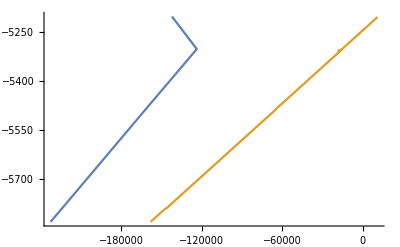

```mathematica
Pint={9182.45,9227.42,9227.44,9309.95,9447.09,9465.89};
Pext={9133.74,9275.62,9275.71,9536.04,9968.76,10028.06};
AxialForce={-142314,-123739,-123739,-161605,-224146,-232808};
Ti={93.83,90.29,90.29,97.44,109.31,110.94};
Tp={93.83,90.29,90.29,97.44,109.31,110.94};
L={5203.03,5302.97,5303.03,5486.40,5791.20,5832.96};
stress=Table[{AxialForce[[i]],-L[[i]]},{i,1,Length[L]}];

tablePi=Table[{Pint[[i]],L[[i]]},{i,1,Length[L]}];
tablePe=Table[{Pext[[i]],L[[i]]},{i,1,Length[L]}];
tableTi=Table[{Ti[[i]],L[[i]]},{i,1,Length[L]}];
tableTp=Table[{Tp[[i]],L[[i]]},{i,1,Length[L]}];
n=100;
PiData=ExpandTable[tablePi,n];
PeData=ExpandTable[tablePe,n];
TiData=ExpandTable[tableTi,n];
TpData=ExpandTable[tableTp,n];

Lcement=5203;
Ltotal=5832;
young=3 10^7;
nu=0.3;
pipedatavec={
{9.875,8.539,young,nu,66.9,5203,5832,125000}
};
ax=ComputeAxialStress[PiData,PeData,pipedatavec,Lcement,Ltotal,TiData,TpData];
ListLinePlot[{stress,ax},PlotRange->All]
```